# Project report

## Timing issues

D Malan

Department of Chemistry
University of Pretoria

19 February 2020

## Introduction

Attempts to improve the SFC×GC software written in LabVIEW seems to have introduced issues unrelated to the problems they solved. The first problem I noticed was the temperature controller wildly fluctuating. The second one was missing information on the

## Experimental

I attempted an SFC×GC run of a spiked diesel. The run was interrupted by a power cut.

### Sample

10 % Aromatics in diesel Total™ 50 ppm.

## Calculations

## Results & Discussion.

### Non-deterministic operating system.

First my usual complaint about a non-deterministic operating system:

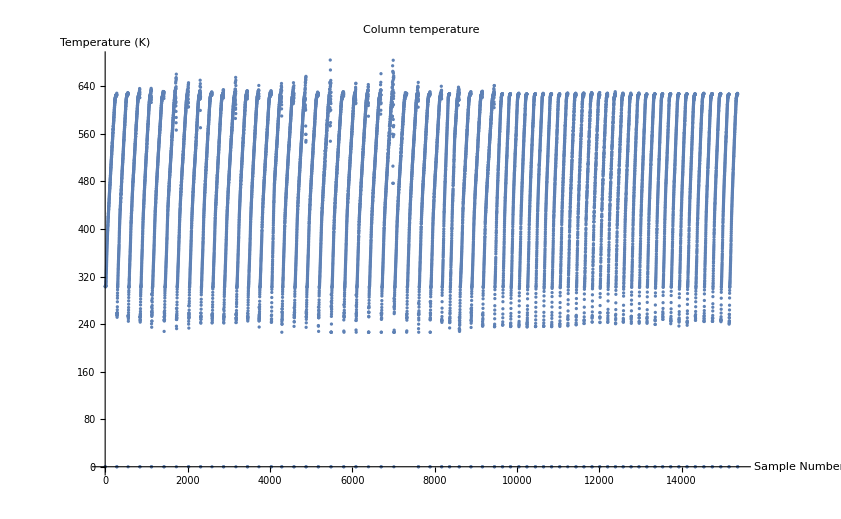

```mathematica
ListPlot[data[[All,12]]
, PlotLabel->"Column temperature"
, AxesLabel->{"Sample Number","Temperature (K)"}
 ]
```

### Controller issues

The temperature controller gave some serious problems when the set point was stable. It would slam between full power and zero power, until at some point the temperature was high enough above the set point to stop this behaviour. Then the heater would cool until it was below the set point, but the moment power

I thought it might have something to do with the low minimum power (0.6 V), because near this value the indicated temperature is fairly dependent on the applied power. Increasing this value to 1.2 V (the safe value it sets after an over-temperature  event), did not solve the problem: it just increased the time it took to cool down.

There' s a rate-limiting setting. Setting this value to a low value (0.001 V/s) reduced the problem, but it also made the controller quite sluggish: it would not be fast enough for the fast GC.

When the indicated temperature was far below the set point this behaviour was not exhibited. This meant that the fast GC runs were quite successful, with only the occasional slamming during the hold at the top of the temperature program.

This is just anecdotal, but it seems that the slamming was less during the later part of the chromatogram, when the computer was busier and stole processor time from the SFC×GC. This can be interpreted as a busier computer causing slower loops, which increased the threshold of the slamming behaviour trigger.  I’ve seen such slamming before, but it always disappeared.

I had removed an “unnecessary” 20 ms delay time in the PID controller. I suspect that this was a hack put in place to prevent the slamming: it has no other obvious function.

During slamming the indicated temperature fluctuates wildly. This cannot be reality: while it’s possible that the coaxial heater can heat up very rapidly, I find it very hard to believe that the temperature can drop by 200 K between one measurement and the next. This means that the slamming is not caused by a fault in the controller, but by a fault in measurement. It is possible that a fault in the controller can induce a fault in measurement, but that still means that the measurement is faulty.

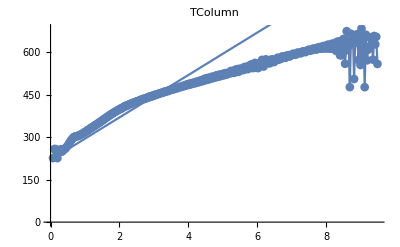

That the measurement can be faulty during rapid changes to the power setting is not a surprise: this happens every time at the end of a GC run, when the set point changes in a single step from 350 °C to, say 30 °C. This produces a large change in the indicated temperature, sometimes exceeding the Absolute Maximum safety temperature. There’s a good chance that this is an electronic problem.

### Missing data

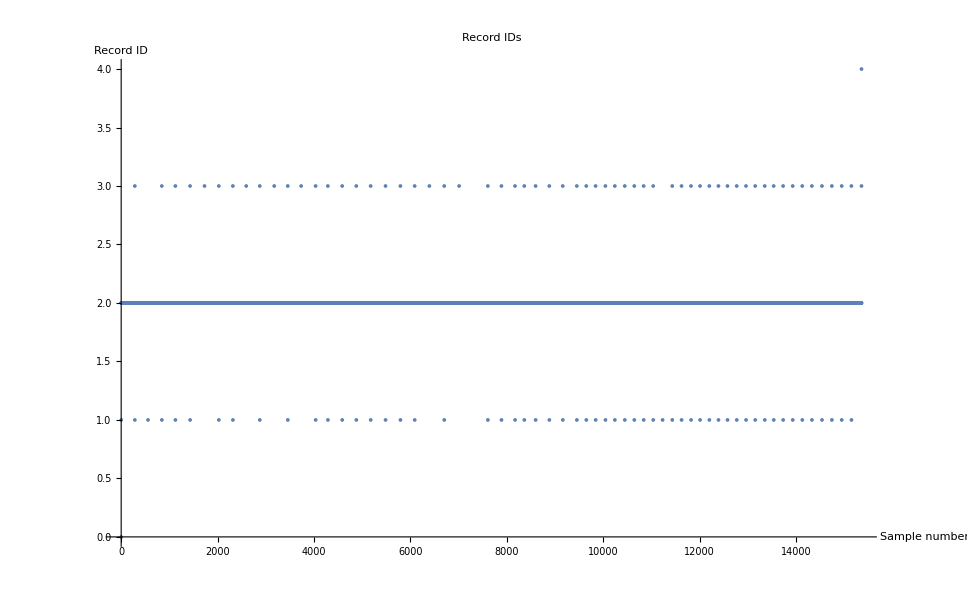

```mathematica
ListPlot[data[[All, 1]]
,PlotLabel->"Record IDs"
,AxesLabel->{"Sample number","Record ID"}
]
```

Every measurement done during a GC run is recorded, and a few others too. The ID of the record, which is the first item, says what the record represent. There are 4 types:
ID = 0 Start time of SFC run
ID = 1 Start time of GC run
ID = 2 Time of GC record
ID = 3 End time of GC run
ID = 4 End time of SFC run

The changes between SFC states determine which ID is recorded. This is done by reading the local variables of the SFC state indicators on the VI front panel. So far I’ve been lucky, and the system worked reliably. But now that I’ve removed the fixed 200 ms time for the loop, it seems that in some cases the the SFC indicators changes faster than the measurement loop can detect. (I think this is a good thing.) I am a bit surprised that I haven’t seen it happen before, because it is quite possible for this to happen at any time.

### Peak retention time repeatability

If the peak retention times are highly repeatable, the  chromatogram will be very pretty. But it will take some work to recover the 2D chromatogram from the data.  So I visually looked at the repeatability of peaks in the 1D chromatograms and saw that the changes in the peak position between consecutive GC runs are very small. From memory the changes are smaller than in other chromatograms. In any event, it seems to be in the 10 - 20 ms range, which is what we advertised in the RSI paper.

### Chromatogram shapes

The higher temperature ramp rates at the start of the chromatograms certainly yielded sharper peaks for the early-eluting aromatics. I do feel, however, that it can be tweaked a bit to allow slower elution of the HC hump. The previous temperature program  gave very pretty peaks over the hump. The fast elution seems to squash things together: the whole thing is over in 10 seconds. I can do this by lowering the start temperature of the main ramp.

## Conclusion

Changes to the SFC×GC software have exposed issues with event timing and temperature control.

## Recommendations

Examine the cause of error in indicated temperature upon sharp changes in set point.

Determine the minimum rate of set point change which does not cause errors in indicated temperature.

Recover the data generated by today’s run and make a pretty chromatogram to show the sharp GC peaks.

Use FIFOs for communicating data between loops, instead of local variables.